```mathematica
Clear["Global`*"]
```

```mathematica
AU2cm:=1.496*10^13
pc2cm:=3.08*10^(18)

(*pc2cm*4.84814*10^(-6)/(AU2cm)*)
```

```mathematica
(*V band mag of a sun-like star*)
(*Distance in cm*)
mVsun :=-26.8 (*http://astro.wku.edu/labs/m100/mags.html*)
mVstar[Dstcm_]:=mVsun+2.5*Log10[(Dstcm/AU2cm)^2]

(**)
(*Gaia specs and fitting formula from: (updated April/2022) 
https://www.cosmos.esa.int/web/gaia/science-performance#astrometric%20performance*)
(*Vmag -> Gmag From Evans+ 8/2018 -- https://arxiv.org/pdf/1804.09368.pdf*)

VmIcSun:=0.688 (*Diff in Vband and I band color of ths Sun, See: Table 2: https://academic.oup.com/mnras/article/367/2/449/1011059*)
(*Plot[Gmag[mVstar[10^Dst*pc2cm],VmIc],{Dst,1,4}]*)

(*from Jordi+2010*)
GmagOld[Vmag_,VmIc_]:=Vmag-0.0257-0.0924*(VmIc)-0.1623*(VmIc)^2+0.0090*(VmIc)^3
(*DD:2019 from Evans+8/2018*)
Gmag[Vmag_,VmIc_]:=Vmag-0.01746+0.008092*(VmIc)-0.2810*(VmIc)^2+0.03655*(VmIc)^3
(*Vmag-0.01746+0.008092*(VmIc)-0.2810*(VmIc)**2+0.03655*(VmIc)**3*)


ZfacNEW[Vmag_, VmIc_]:=Max[10^(0.4*(13.0-15.)), 10^(0.4*(Gmag[Vmag,VmIc]-15.))]


(*https://www.cosmos.esa.int/web/gaia/science-performance#astrometric%20performance*)
(*factors of 1.2 and 2.15 are a margin(just making it worse to be safe) and sky average factors from https://arxiv.org/pdf/1411.1173.pdf*)
(*Note: 
Margin has been reduced from 1.2 to 1.1 -- see Section1 at gaia science case website above -- chanign 1.2 margin factor to 1.1
*)
(*0.527 factor is for 10 yr mission*)
(*0.749 factor is for 5 yr mission*)
(*they are ~sqrt(2) diff, which is accounted for by the number of visists increasing by 2 between 5 and 10 yrs,
that is, sqrt(70)*0.749 = 6.267 changes  to sqrt(140)0.527 = 6.235*)

(*In terms of Vmag*)
MinResMissionEnd[Vmag_,VmIc_]:=0.527*Sqrt[40. + 800.*ZfacNEW[Vmag, VmIc] + 30.*(ZfacNEW[Vmag, VmIc])^2]

MinResSnglScan[Vmag_,VmIc_,SNR_]:=SNR*Sqrt[140]/2.15/1.1*0.527*Sqrt[40. + 800.*ZfacNEW[Vmag, VmIc] + 30.*(ZfacNEW[Vmag, VmIc])^2]

(*In terms of Distance and SNR !specificaly for Sun-like stars!*)
MinResMEndDst[Dst_]:=0.527*Sqrt[40. + 800.*ZfacNEW[mVstar[Dst], VmIcSun] + 30.*(ZfacNEW[mVstar[Dst], VmIcSun])^2]

MinResSSDst[Dst_, SNR_]:=SNR*Sqrt[140]/2.15/1.1*0.527*Sqrt[40. + 800.*ZfacNEW[mVstar[Dst], VmIcSun] + 30.*(ZfacNEW[mVstar[Dst], VmIcSun])^2]
```

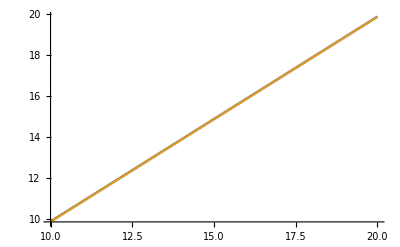

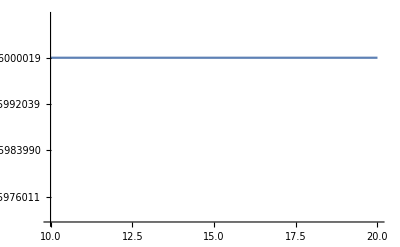

```mathematica
(*diff in two diff G-V conversions*)
Plot[{Gmag[Vmag,VmIcSun],GmagOld[Vmag,VmIcSun]}, {Vmag,10,20}]
Plot[Gmag[Vmag,VmIcSun]-GmagOld[Vmag,VmIcSun], {Vmag,10,20}]
```

-26.9002

14.6049

14.6049

19.6049

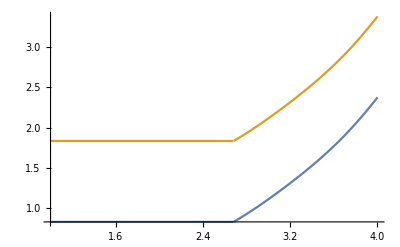

```mathematica
(*Plot[{Log10[MinResMEndDst[10^Dst*pc2cm]],Log10[MinResNew[mVstar[10^Dst*pc2cm],VmIc]],Log10[MinResSSDst[10^Dst*pc2cm,3]]},{Dst,1,4}]*)
Gmag[mVstar[0.5*10^(-5)*pc2cm],VmIcSun]
Gmag[mVstar[10^3*pc2cm],VmIcSun]
Gmag[mVstar[10^3*pc2cm],VmIcSun]
Gmag[mVstar[10^4*pc2cm],VmIcSun]
Plot[{Log10[MinResMEndDst[10^Dst*pc2cm]],Log10[MinResSSDst[10^Dst*pc2cm,2]]},{Dst,1,4}]
```

```mathematica
(*Plot[mVstar[10^Dst*pc2cm],{Dst,1,4}]
mVstar[10*pc2cm]*)
```

```mathematica
MinResMEndDst[10*pc2cm]
```

6.82144